```mathematica
rawData=Import["Desktop/Quant.Trading/round-1-island-data-bottle/prices_round_1_day_-1.csv"];
```

```mathematica
parseString[s_String]:=Module[{clean,data},clean=StringReplace[s,"_"->""];
data=StringSplit[clean,";"];
data/. ""->Null]//ToExpression;

data=(parseString/@(rawData//Flatten))//ToExpression;
```

```mathematica
{Range[Length@data[[1]]],data[[1]]}//Transpose
```

{{1,day},{2,timestamp},{3,product},{4,bidprice1},{5,bidvolume1},{6,bidprice2},{7,bidvolume2},{8,bidprice3},{9,bidvolume3},{10,askprice1},{11,askvolume1},{12,askprice2},{13,askvolume2},{14,askprice3},{15,askvolume3},{16,midprice},{17,profitandloss}}

```mathematica
tab=data[[2;;,3]]//Union
typedData[mercType_,dataType_]:= data[[
Position[data,mercType][[;;,1]],
dataType]];
```

{KELP,RAINFORESTRESIN,SQUIDINK}

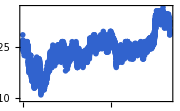
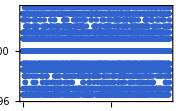
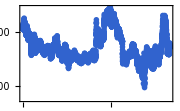

```mathematica
Table[
ListPlot[typedData[k,16]//Evaluate,ImageSize->Small],{k,tab}]
```

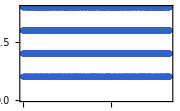
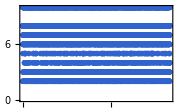
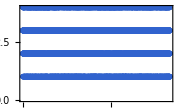

```mathematica
Table[
ListPlot[typedData[k,10]-typedData[k,4],ImageSize->Small],{k,tab}]
```